## Header

```mathematica
<<EEGPack`;
subject="0207";
```

<<KazukazuM version (PacletInfo.m not found) loaded on: Tue 12 Jun 2012 05:05:56>>

```mathematica
dataDirectory="V:\\_results.EEG\\0201_0250\\";
SetDirectory[dataDirectory]
```

V:\_results.EEG\0201_0250

## Data Import (Adjust for each subject)

```mathematica
files=FileNames[subject <> "*"];data=Flatten[ ImportEEG[#,Verbose->True]& /@ files ];
```

>> 0207.01.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 15104} (Length 59 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.0.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 1280} (Length 5 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.11.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 1280} (Length 5 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.12.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 2304} (Length 9 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.13.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 1792} (Length 7 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.14.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 1280} (Length 5 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.15.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 4096} (Length 16 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.16.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 2048} (Length 8 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.17.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 1792} (Length 7 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

>> 0207.1.edf
 PatientID -> 7052975 M 06-FEB-2008 Peyton_Rigsbee
 SampleRate -> 256
 Dimensions: {32, 3072} (Length 12 seconds)
 Channels = {Fp1, Fp2, F3, F4, C3, C4, P3, P4, O1, O2, F7, F8, T3, T4, T5, T6, A1, A2, Fz, Cz, Pz, 22, 23, 24, ECG EKG, 27, 28, 29, 30, 31, 32, Photic}

```mathematica
data=Delete[ data,  List /@ {3,4,8,9,10}  ];
```

```mathematica
Length[data]
```

5

## EEG Montage

```mathematica
EEGChannels::usage="Component of EEGMontage, denotes montage channels.";
EEGChannelColors::usage="Component of EEGMontage, denotes colors assigned to montage channels.";
```

```mathematica
EEGMontage["DoubleBanana"]:={
EEGChannels->{{"Fp1","F7"},{"F7","T3"},{"T3","T5"},{"T5","O1"},
 {"Fp2","F8"},{"F8","T4"},{"T4","T6"},{"T6","O2"},
 {"Fp1","F3"},{"F3","C3"},{"C3","P3"},{"P3","O1"},
 {"Fp2","F4"},{"F4","C4"},{"C4","P4"},{"P4","O2"},
 {"Fz","Cz"},{"Cz","Pz"}},
EEGChannelColors->Join[Table[Darker[Blue],{4}],Table[Darker[Red],{4}],Table[Darker[Blue],{4}],Table[Darker[Red],{4}],Table[Darker[Green],{4}]]
};
```

```mathematica
EEGChannels /. EEGMontage["DoubleBanana"]
```

{{Fp1,F7},{F7,T3},{T3,T5},{T5,O1},{Fp2,F8},{F8,T4},{T4,T6},{T6,O2},{Fp1,F3},{F3,C3},{C3,P3},{P3,O1},{Fp2,F4},{F4,C4},{C4,P4},{P4,O2},{Fz,Cz},{Cz,Pz}}

```mathematica
EEGChannelColors /. EEGMontage["DoubleBanana"]
```

{RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[2/3,0,0],RGBColor[2/3,0,0],RGBColor[2/3,0,0],RGBColor[2/3,0,0],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[2/3,0,0],RGBColor[2/3,0,0],RGBColor[2/3,0,0],RGBColor[2/3,0,0],RGBColor[0,2/3,0],RGBColor[0,2/3,0],RGBColor[0,2/3,0],RGBColor[0,2/3,0]}

## Overlay Stack

```mathematica
EEGStackTraces::usage="Option for EEGPlot, how high to stack traces.";
EEGPageLength::usage="Option for EEGPlot, how long to make EEGPages.";
```

```mathematica
Options[EEGPlot] = 
{ BandpassFilter->None, EEGStackTraces->100, EEGMontage -> "DoubleBanana", EEGPageLength->10,

PlotRange -> All,  PlotRangePadding -> None, AxesOrigin -> {0, 0}, ImageSize -> Automatic, GridLines -> Automatic, 
PlotStyle->Automatic,BaseStyle->{FontFamily->"Arial",FontSize->8},Axes->{False,True},Ticks->Automatic,
AspectRatio -> Automatic, Axes -> False};
```

```mathematica
Options[EEGPlotImpl] =Options[EEGPlot] ;
```

```mathematica
EEGPlotImpl[tempPlotData_, tempMaxMin_, tempLength_, 
			opMontage_, opChannels_,opEEGStackTraces_, sampleRate_, 
			opts : OptionsPattern[]] :=
	Module[{tempOptions,opPlotStyle,opColors},

	(*====Option Handling for Plot====*)
	tempOptions = {opts};
	If[OptionValue[GridLines] == Automatic,
		PrependTo[tempOptions, GridLines -> {Range[0, tempLength, 1], None}],
	];
	If[OptionValue[Ticks] == Automatic,
		PrependTo[tempOptions, Ticks -> 
			{None,Table[{opEEGStackTraces*(n),(#[[1]]<>"-"<>#[[2]])&[opChannels[[-n]]]},
			{n,1,Length[opChannels]}]}
		]
	];
	opPlotStyle=OptionValue[PlotStyle];
	opColors=(EEGChannelColors /. opMontage);
	If[opPlotStyle === Automatic, PrependTo[tempOptions, PlotStyle->opColors],
		If[Head[opPlotStyle] === Opacity, PrependTo[tempOptions, PlotStyle-> (Directive[#,opPlotStyle]& /@ opColors)],
			If[Head[opPlotStyle] === Directive, PrependTo[tempOptions, PlotStyle-> (Join[Directive[#],opPlotStyle]& /@ opColors)]
	]]];
(*Print[tempOptions];*)
	If[OptionValue[ImageSize] == Automatic, PrependTo[tempOptions, ImageSize -> 8*72*(tempLength/10)]];
	If[OptionValue[AspectRatio] == Automatic, PrependTo[tempOptions, AspectRatio -> 10*tempMaxMin/2000/tempLength]];

	tempOptions = Join[tempOptions,
			 FilterRules[Options[EEGPlotImpl], Except[tempOptions]],
			 {DataRange->{0,tempLength}}
	];
	tempOptions = FilterRules[tempOptions, Options[ListLinePlot]];
(*Print[tempOptions];*)

	(*====Plot====*)
	ListLinePlot[tempPlotData, tempOptions]
];
```

```mathematica
EEGPlot[eegData_EEGData, opts : OptionsPattern[]] :=
	Module[{tempPlotData, sampleRate, tempMaxMin, tempLength,
	 opChannels, opBandpassFilter, opMontage, opEEGStackTraces, opEEGPageLength},

	(*====Option Processing====*)
	opMontage=OptionValue[EEGMontage];
		opMontage=Switch[Head[opMontage], List, opMontage, String, EEGMontage[opMontage], _, EEGMontage["DoubleBanana"]];
	opChannels=(EEGChannels /. opMontage);
	opEEGStackTraces=OptionValue[EEGStackTraces];
	opBandpassFilter=OptionValue[BandpassFilter];
	opEEGPageLength=OptionValue[EEGPageLength];

	(*====Data Formatting====*)
	sampleRate = Options[eegData, SampleRate][[1,2]];
	tempPlotData = eegData /@ (opChannels);
	If[opBandpassFilter =!= False && opBandpassFilter =!= None, 
		tempPlotData = FilterBandpass[tempPlotData, opBandpassFilter, Options[eegData, SampleRate][[1,2]]];
	];
	tempPlotData = StackTraces[tempPlotData, opEEGStackTraces];
	(*tempMaxMin = (Max[#] - Min[#]) & [Flatten[tempPlotData]];*)
	tempMaxMin = opEEGStackTraces * (Length[tempPlotData] + 1);
	tempLength = Length[tempPlotData[[1]]]/sampleRate;

	(*====Divide into Pages and Plot====*)
	If[opEEGPageLength>=tempLength,
		EEGPlotImpl[tempPlotData, tempMaxMin, tempLength, opMontage, opChannels, opEEGStackTraces, sampleRate, opts],
		EEGPlotImpl[#, tempMaxMin, Length[#[[1]]]/sampleRate, opMontage, opChannels, opEEGStackTraces, sampleRate, opts]&
			/@ Transpose[Partition[#, opEEGPageLength*sampleRate]& /@ tempPlotData, {2,1,3}]
	]
];
```

```mathematica
Show @@ EEGPlot[data[[1]],PlotStyle->Opacity[0.25]]
```

-Graphics-

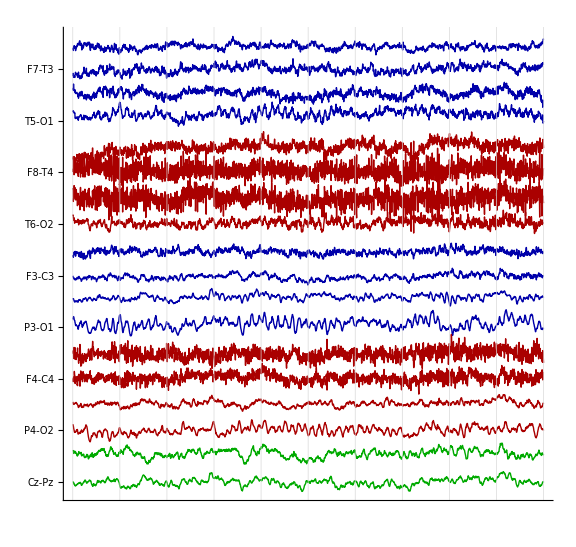
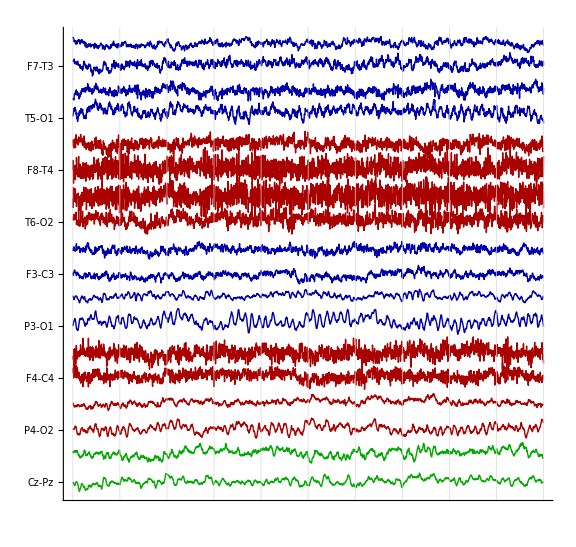
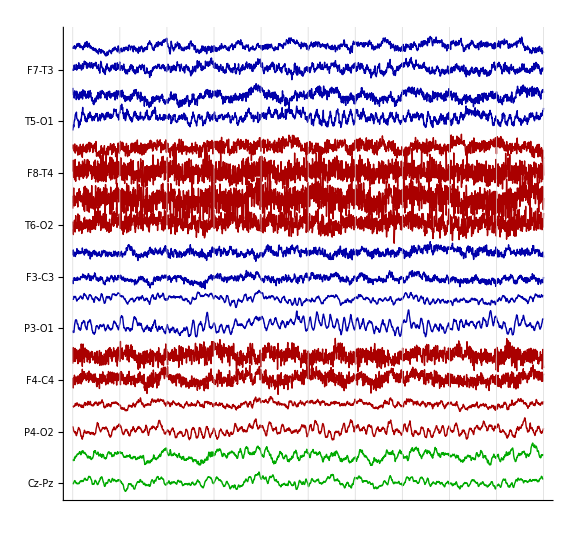
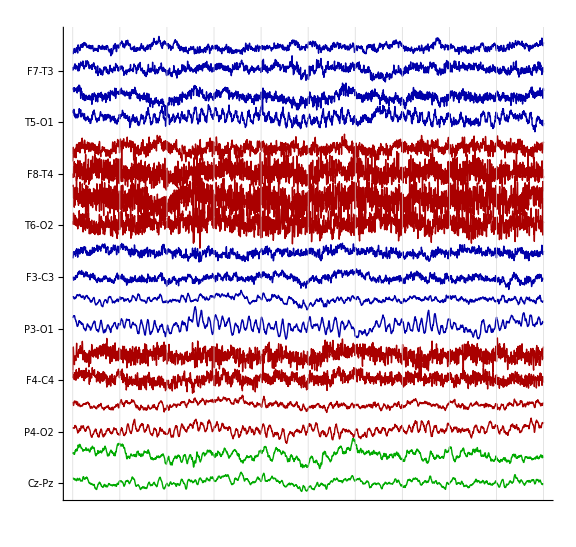
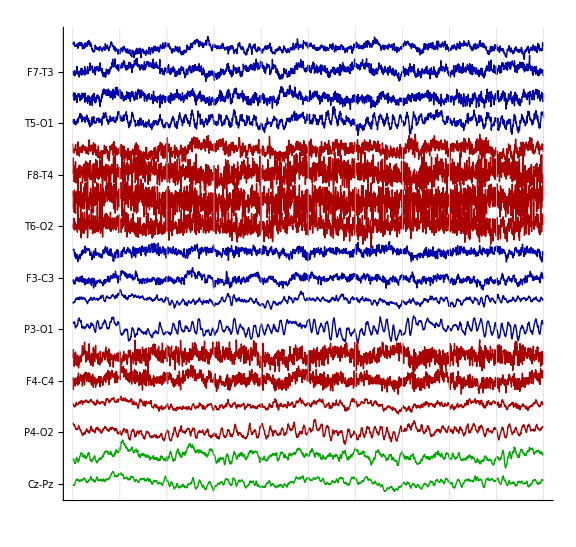

```mathematica
EEGPlot[data[[1]]]
```

## Backup Copies

```mathematica
plotdata=data[[1]];
temp=StackTraces[FilterBandpass[plotdata /@ MontageDoubleBanana, {40,1},250],100];
```

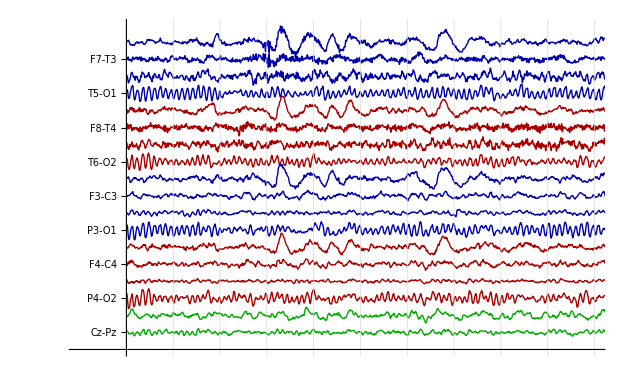

```mathematica
ListLinePlot[temp,PlotStyle->Join[Table[Darker[Blue],{4}],Table[Darker[Red],{4}],Table[Darker[Blue],{4}],Table[Darker[Red],{4}],Table[Darker[Green],{4}]],
PlotRange->{{-250,2500},Automatic},
BaseStyle->{FontFamily->"Arial",FontSize->8},
GridLines->{Table[n,{n,250,2500,250}],None},
Axes->{False,True},
Ticks->{None,Table[{100*(n),(#[[1]]<>"-"<>#[[2]])&[MontageDoubleBanana[[-n]]]},{n,1,Length[MontageDoubleBanana]}]}
]
```

```mathematica
EEGPlot[eegData_EEGData, opts : OptionsPattern[]] :=
	Module[{tempPlotData, tempMaxMin, tempLength,
		tempOptions, tempOptionsSegment, sampleRate,opBandpassFilter,
		k, tempPlotDataSeg},

	tempPlotData = eegData /@ OptionValue[Montage];
	opBandpassFilter=OptionValue[BandpassFilter];
	If[opBandpassFilter =!= False && opBandpassFilter =!= None, 
		tempPlotData = FilterBandpass[tempPlotData, opBandpassFilter, Options[eegData, SampleRate][[1,2]]];
	];

	tempPlotData = StackTraces[tempPlotData, 100];
	tempMaxMin = (Max[#] - Min[#]) & [Flatten[tempPlotData]];
	sampleRate = SampleRate /. Cases[eegData, x_ /; Head[x] === Rule];
	tempLength = Length[tempPlotData[[1]]]/sampleRate;

	tempOptions = {opts};
	If[OptionValue[GridLines] == Automatic,
		PrependTo[tempOptions, 
		GridLines -> {Range[0, #2, sampleRate]&, None}]
	];
  
	If[tempLength <= 10,
		If[OptionValue[ImageSize] == Automatic,
			PrependTo[tempOptions, ImageSize -> 8*72*(tempLength/10)]];
		If[OptionValue[AspectRatio] == Automatic,
			PrependTo[tempOptions, AspectRatio -> 10*tempMaxMin/2000/tempLength]];
		tempOptions = 
			Join[tempOptions,
					FilterRules[Options[EEGPlot], Except[tempOptions]]
			];
		tempOptions = FilterRules[tempOptions,Options[ListLinePlot]];
		Print[Rasterize[ListLinePlot[tempPlotData, tempOptions]]],

		For[k = 1, k <= Ceiling[tempLength/10], k++,
			tempOptionsSegment = tempOptions;

			tempPlotDataSeg = 
				tempPlotData[[All, 
						(k - 1)*10*sampleRate + 1 ;;
						Min[k*10*sampleRate, Length[ tempPlotData[[1]] ] ]
							]];

			If[OptionValue[ImageSize] == Automatic,
				PrependTo[tempOptionsSegment, 
				ImageSize -> 8*72*((Length[tempPlotDataSeg[[1]]]/sampleRate)/10)]
			];
			If[OptionValue[AspectRatio] == Automatic,
				PrependTo[tempOptionsSegment, 
				AspectRatio -> 
					10*tempMaxMin/2000/(Length[tempPlotDataSeg[[1]]]/sampleRate)]
			];
			(*If[OptionValue[PlotRange]==Automatic,
				PrependTo[tempOptionsSegment, 
				PlotRange->{(k-1)*10*sampleRate+{1,Length[tempPlotDataSeg[[1]]]}, All}]
			];*)

			tempOptionsSegment = 
				Join[tempOptionsSegment, 
					FilterRules[Options[EEGPlot], Except[tempOptionsSegment]]
				];
    		tempOptionsSegment = FilterRules[tempOptionsSegment,Options[ListLinePlot]];
			Print[Rasterize[ListLinePlot[tempPlotDataSeg, tempOptionsSegment]]];
		];
	](*If[tempLength < 10,*)
];
```